## Маевский А. В. Лабораторная работа №7 : Статистический анализ в системе Mathematica

## Задание 1: Элементарная описательная статистика

```mathematica
data=RandomReal[{1,100},12](*12 случайных вещественных чисел от 1 до 100*)
```

{47.5373,98.6182,88.0426,22.1703,84.7006,49.1923,57.7395,83.3157,65.8374,20.7514,22.4755,89.5702}

```mathematica
Mean[data] (*Находит среднее значение*)
```

60.8292

```mathematica
Median[data](*Находит значение середины*)
```

61.7885

```mathematica
Max[data](*Находит максимальное значение*)
```

98.6182

```mathematica
Variance[data](*Находит дисперсию (меру разброса значений случайной величины относительно средней арифметической)*)
```

817.143

```mathematica
StandardDeviation[data](*Находит среднеквадратичное отклонение(если из дисперсии извлечь квадратный корень, получится среднеквадратичное отклонение)*)
```

28.5857

```mathematica
Quantile[data,1/2](*Находит квантиль (значение, которое заданная случайная величина не превышает с фиксированной вероятностью) Первый агрумент - набор данных,второй - число q в диапазоне от 0 до 1*)
```

57.7395

```mathematica
Quartiles[data](*Находит квантитили для списка*)
```

{35.0064,61.7885,86.3716}

## Задание 2: Работа со статистическими распределениями

```mathematica
PDF[NormalDistribution[μ,σ],x] (*дает функцию плотности вероятности для распределения, оцененного в точке x*)
PDF[NormalDistribution[2,9],6]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/(9 ⅇ^(8/81) √(2 π))

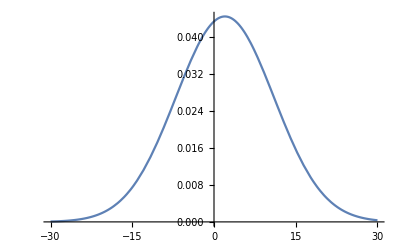

```mathematica
Plot[PDF[NormalDistribution[2,9],x],{x,-30,30}]
```

```mathematica
CharacteristicFunction[NormalDistribution[μ,σ],t] (*дает характеристическую функцию для распределения в зависимости от переменной t*)
CharacteristicFunction[CauchyDistribution[μ,σ],t]  (*распределени Коши*)
```

ⅇ^(ⅈ t μ-(t^2 σ^2)/2)

ⅇ^(ⅈ t μ-t σ Sign[t])

```mathematica
(*дает среднее значение успеха в 300 независимых 
испытаниях, где вероятность успеха в каждом испытании равна 0.3*)
Mean[BinomialDistribution[300,.3]]
```

90.

```mathematica
Moment[PoissonDistribution[μ],n](*дает n-й момент выборки элементов в списке*)
```

Piecewise[{{BellB[n,μ], n≥0}, {0, True}}]

```mathematica
(*дает псевдослучайную переменную из символического распределения dist.*)
RandomVariate[GeometricDistribution[1/3],20]
```

{0,5,2,5,0,0,3,0,5,3,6,0,0,0,1,1,5,2,4,4}

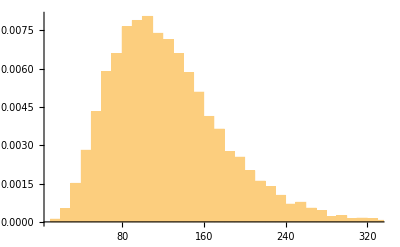

```mathematica
data=RandomVariate[GammaDistribution[5,25],10000];
hist=Histogram[data,Automatic,"ProbabilityDensity"]
```

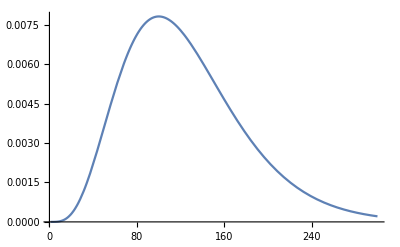

```mathematica
pl=Plot[PDF[GammaDistribution[5,25],x],{x,1,300}]
```

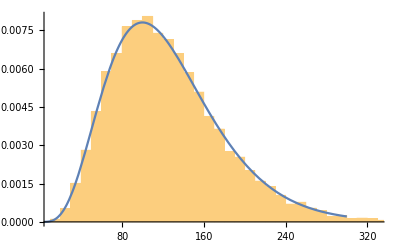

```mathematica
Show[hist,pl]
```

## Задача: Население 2-х стран

```mathematica
populationData={Callout[CountryData["Romania",{"Population",{1960,2020}}],"Romania",{Scaled[0.4],Above}],
Callout[CountryData["Belarus",{"Population",{1960,2020}}],"Belarus",Scaled[0.6]]};
options={ImageSize->500,PlotStyle->72,Filling->{1->{2},2->Axis},FillingStyle->72};
Grid[{{DateListPlot[populationData,options]}}]
```

-Graphics-

CountryData::notprop: {"Area"} is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

CountryData[Romania,{Area}]

## Задача: Добавить цвета на фото

```mathematica
Colorize[-Graphics-]
```

-Graphics-